{1,2,3,4}

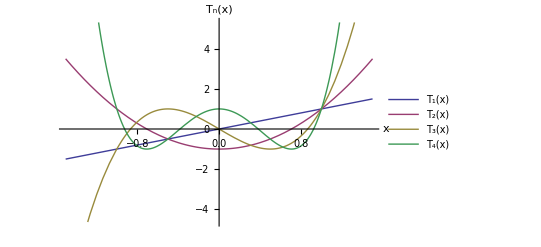

```mathematica
a = Table[i,{i,4}]
p = Plot[ChebyshevT[#,x] &/@ a // Evaluate ,{x,-1.5,1.5}, AxesLabel -> {x, "T_n(x)"}, PlotLegends -> Placed[ Row[{Subscript["T",#],"(x)"}] &/@ a, {Right,Bottom}]]
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "figures\\ece1229" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229

```mathematica
peeters`exportForLatex["ChebychevFig1", p]
```

{C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/ChebychevFig1.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/ChebychevFig1pn.png}